# Math IA plot

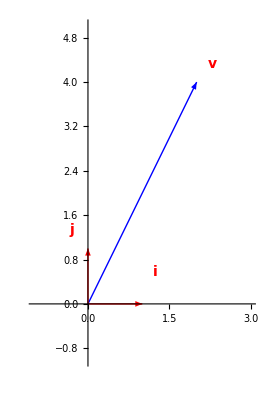

```mathematica
Graphics[{Red,Arrow[{{0,0},{1,0}}],Blue,Arrow[{{0,0},{2,4}}],Red,Arrow[{{0,0},{0,1}}],Text[Style["i",14,Bold],{1.2,0.7},{-1,1}],Text[Style["j",14,Bold],{-0.3,1.2},{0,-1}],Text[Style["v",14,Bold],{2.2,4.2},{-1,-1}]},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,3},{-1,5}},Ticks->Automatic]
```

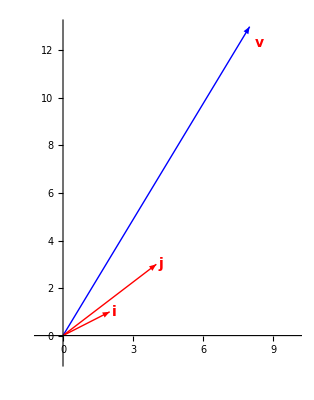

```mathematica
Graphics[{Red,Arrow[{{0,0},{2,1}}],Blue,Arrow[{{0,0},{8,13}}],Red,Arrow[{{0,0},{4,3}}],Text[Style["i",14,Bold],{2.1,1},{-1,0}],Text[Style["j",14,Bold],{4.1,3},{-1,0}],Text[Style["v",14,Bold],{8.2,12},{-1,-1}]},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,10},{-1,13}},Ticks->Automatic]
```

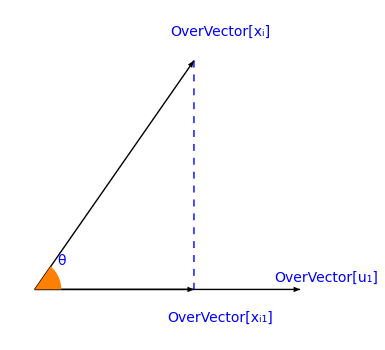

```mathematica
(*Define the vectors*)a={3,4};
b={5,0};

(*Calculate the projection of a onto b*)
proj=(a.b)/(b.b) b;

(*Create the plot*)
Graphics[{Arrow[{{0,0},a}],(*Vector a*)Arrow[{{0,0},b}],(*Vector b*)Arrow[{{0,0},proj}],(*Projection of a on b*)Blue,Text[Style["θ",14],{0.5,0.5}],(*Angle theta*)Orange,Disk[{0,0},0.5,{0,ArcTan@@a}],(*Angle arc*)Blue,Dashed,Line[{a,proj}],(*Perpendicular line*)Text[Style[Overscript[Subscript["x","i"],"→"],14,Blue],a+{0.5,0.5}],Text[Style[Overscript[Subscript["u","1"],"→"],14,Blue],b+{0.5,0.2}],Text[Style[Overscript[Subscript["x","i1"],"→"],14,Blue],proj+{0.5,-0.5}]}]
```

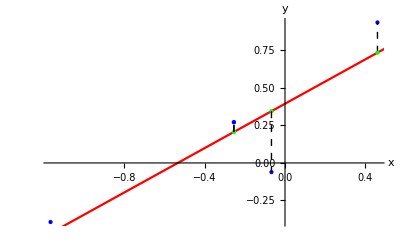

```mathematica
(*Define the points*)points={{0.460179 ,0.935301},{-1.166792,-0.393216},{-0.254307, 0.271042},{-0.254307, 0.271042},{-0.067382,-0.061087}};

(*Calculate the best fit line*)
fit=LinearModelFit[points,x,x];

(*Define the line function*)
lineFunc[x_]=fit[x];

(*Project the points onto the line*)
projections=points/. {x_,y_}:>{x,lineFunc[x]};

(*Create the plot*)
Show[ListPlot[points,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"x","y"}],Plot[fit[x],{x,-2,1},PlotStyle->{Red}],ListPlot[projections,PlotStyle->{Green,PointSize[Medium]}],Graphics[{Dashed,Line[{{#,lineFunc[#]},{#,#2}}]&@@@points}]]
```

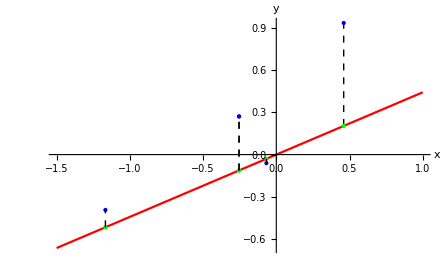

```mathematica
(*Define the points*)points={{0.460179,0.935301},{-1.166792,-0.393216},{-0.254307,0.271042},{-0.254307,0.271042},{-0.067382,-0.061087}};

(*Calculate the best fit line passing through the origin*)
fit=Fit[points,{x},x];

(*Define the line function*)
lineFunc[x_]=fit;

(*Project the points onto the line*)
projections=points/. {x_,y_}:>{x,lineFunc[x]};

(*Create the plot*)
Show[ListPlot[points,PlotStyle->{Blue,PointSize[Large]},AxesLabel->{"x","y"}],Plot[fit,{x,-1.5,1},PlotStyle->{Red}],ListPlot[projections,PlotStyle->{Green,PointSize[Medium]}],Graphics[{Dashed,Line[{{#,lineFunc[#]},{#,#2}}]&@@@points}],PlotRange->All]
```